```mathematica
Convolve[(HeavisideTheta[t]-HeavisideTheta[t-0.01])+200*(t-0.011)*(HeavisideTheta[t-0.011]-HeavisideTheta[t-0.016]),1000*Exp[-1000*t]*HeavisideTheta[t],t,x]
```

1000 (200 ⅇ^(-1000 x) (((35.5444-2.45941×10^-13 ⅈ)+ⅇ^(1000 x) (0.000012-0.001 x)) HeavisideTheta[-0.016+x]+((0.0598741+7.40579×10^-16 ⅈ)+ⅇ^(1000 x) (-0.000012+0.001 x)) HeavisideTheta[-0.011+x])-(0.001-22.0265 ⅇ^(-1000 x)) HeavisideTheta[-0.01+x]+((1-ⅇ^(-1000 x)) HeavisideTheta[x])/1000)

```mathematica
V[t_]:=Exp[-1000*t]*(Exp[10]-1+200*(t-0.011)*(Exp[16]-Exp[11]))
```

```mathematica
V[0.0002]
```

-1.55908×10^7

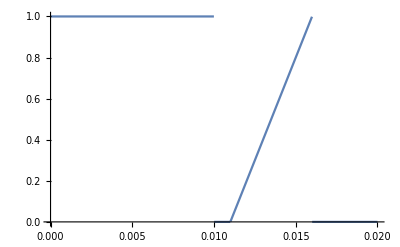

```mathematica
Plot[(HeavisideTheta[t]-HeavisideTheta[t-0.01])+200*(t-0.011)*(HeavisideTheta[t-0.011]-HeavisideTheta[t-0.016]),{t,0,0.02}]
```

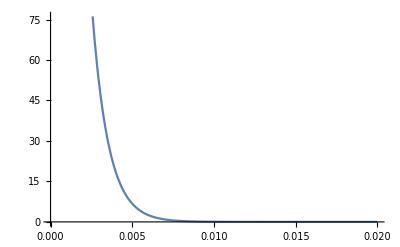

```mathematica
Plot[1000*Exp[-1000*t]*HeavisideTheta[t],{t,0,0.02}]
```

```mathematica
Convolve[HeavisideTheta[t]-HeavisideTheta[t-0.01],1000*Exp[-1000*t]*HeavisideTheta[t],t,x]
```

1000 (-(0.001-22.0265 ⅇ^(-1000 x)) HeavisideTheta[-0.01+x]+((1-ⅇ^(-1000 x)) HeavisideTheta[x])/1000)

```mathematica
Integrate[1000*Exp[-1000*τ],{τ,t-0.01,t}]
```

22025.5 ⅇ^(-1000. t)

```mathematica
Convolve[200*(t-0.011)*(HeavisideTheta[t-0.011]-HeavisideTheta[t-0.016]),1000*Exp[-1000*t]*HeavisideTheta[t],t,x]
```

200000 ⅇ^(-1000 x) (((35.5444-2.45941×10^-13 ⅈ)+ⅇ^(1000 x) (0.000012-0.001 x)) HeavisideTheta[-0.016+x]+((0.0598741+7.40579×10^-16 ⅈ)+ⅇ^(1000 x) (-0.000012+0.001 x)) HeavisideTheta[-0.011+x])

```mathematica
Integrate[200*τ*1000*Exp[-1000*τ],{τ,0,t-0.011}]
```

0.2+ⅇ^(-1000. t) (119748.-1.19748×10^7 t)

```mathematica
Integrate[200*(τ-0.011)*1000*Exp[-1000(t-τ)],{τ,0.011,t}]
```

-2.4+11974.8 ⅇ^(-1000. t)+200. t

```mathematica
Integrate[200*(τ-0.011)*1000*Exp[-1000(t-τ)],{τ,0.011,0.016}]
```

7.12086×10^6 ⅇ^(-1000. t)

```mathematica
Integrate[200*(t-τ-0.011)*1000*Exp[-1000τ],τ]
```

-200000. ⅇ^(-1000. τ) (-0.000012+0.001 t-0.001 τ)